```mathematica
f[x_]=Exp[x]-1;Lf[z_]=f[z]f''[z]/f'[z]^2; sc[z_]=z-f[z]/f'[z]/(1-Lf[z]);x0=2;nf[x_]=x-f[x]/f'[x]//FullSimplify;
x0=2;
sc[x]//Simplify;
x1=N[sc[x0]];
xn1=N[nf[x0]];
f[x0]+(f'[x0])^2(x-x0)/(f'[x0]-f''[x0](x-x0))//FullSimplify;
(x-x0)f'[x0]+f[x0]//FullSimplify;
grafico1=Plot[{Exp[x]-1, f[x0]+(f'[x0])^2(x-x0)/(f'[x0]-f''[x0](x-x0)),(x-x0)f'[x0]+f[x0] },{x,-5,5}];
```

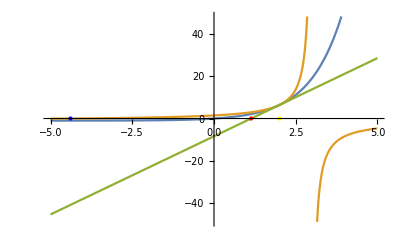

```mathematica
x1=N[sc[x0]];
xn1=N[nf[x0]];
grafico1=Plot[{Exp[x]-1, f[x0]+(f'[x0])^2(x-x0)/(f'[x0]-f''[x0](x-x0)),(x-x0)f'[x0]+f[x0] },{x,-5,5}];
punto0=Graphics[{Yellow,PointSize[Large],Point[{x0,0}]}];
punto1=Graphics[{Blue,PointSize[Large],Point[{x1,0}]}];
puntoN1=Graphics[{Red,PointSize[Large],Point[{xn1,0}]}];
Show[{grafico1,punto0,punto1,puntoN1}]
```

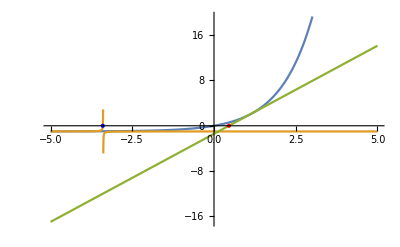

```mathematica
x2=N[sc[x1]];
xn2=N[nf[xn1]];
grafico2=Plot[{Exp[x]-1, f[x1]+(f'[x1])^2(x-x1)/(f'[x1]-f''[x1](x-x1)),(x-xn1)f'[xn1]+f[xn1] },{x,-5,5}];
punto0=Graphics[{Yellow,PointSize[Large],Point[{x0,0}]}];
punto2=Graphics[{Blue,PointSize[Large],Point[{x2,0}]}];
puntoN2=Graphics[{Red,PointSize[Large],Point[{xn2,0}]}];
Show[{grafico2,punto2,puntoN2}]
```

```mathematica
x2=N[sc[x1]];
x2
```

-3.40147

```mathematica
grafico2=Plot[{Exp[x]-1, f[x1]+(f'[x1])^2(x-x1)/(f'[x1]-f''[x1](x-x1)) },{x,-5,2.5}];
```

```mathematica
punto2=Graphics[{PointSize[Large],Point[{x2,0}]}];
```

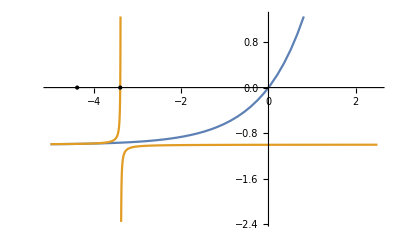

```mathematica
Show[{grafico2,punto2,punto1}]
```

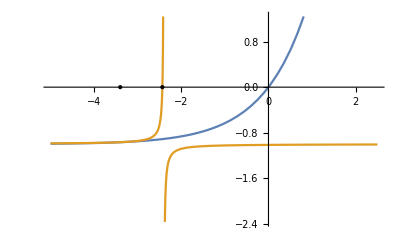

```mathematica
x3=sc[x2];
punto3=Graphics[{PointSize[Large],Point[{x3,0}]}];
grafico3=Plot[{Exp[x]-1, f[x2]+(f'[x2])^2(x-x2)/(f'[x2]-f''[x2](x-x2)) },{x,-5,2.5}];
Show[{grafico3,punto2,punto3}]
```

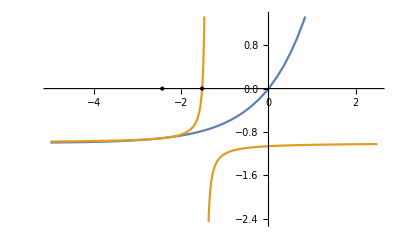

```mathematica
x4=sc[x3];
punto4=Graphics[{PointSize[Large],Point[{x4,0}]}];
grafico4=Plot[{Exp[x]-1, f[x3]+(f'[x3])^2(x-x3)/(f'[x3]-f''[x3](x-x3)) },{x,-5,2.5}];
Show[{grafico4,punto4,punto3}]
```

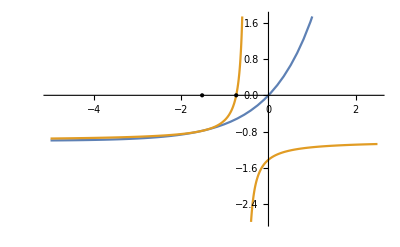

```mathematica
x5=sc[x4];
punto5=Graphics[{PointSize[Large],Point[{x5,0}]}];
grafico5=Plot[{Exp[x]-1, f[x4]+(f'[x4])^2(x-x4)/(f'[x4]-f''[x4](x-x4)) },{x,-5,2.5}];
Show[{grafico3,punto4,punto5}]
```

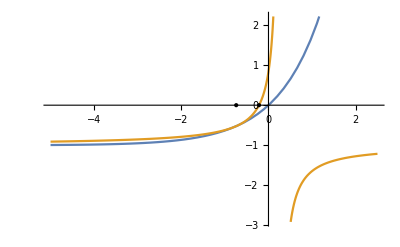

```mathematica
x6=sc[x5];
punto6=Graphics[{PointSize[Large],Point[{x6,0}]}];
grafico6=Plot[{Exp[x]-1, f[x5]+(f'[x5])^2(x-x5)/(f'[x5]-f''[x5](x-x5)) },{x,-5,2.5}];
Show[{grafico6,punto6,punto5}]
```

-0.0220129

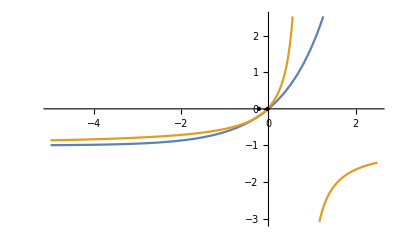

```mathematica
x7=sc[x6];
x7
punto7=Graphics[{PointSize[Large],Point[{x7,0}]}];
grafico7=Plot[{Exp[x]-1, f[x6]+(f'[x6])^2(x-x6)/(f'[x6]-f''[x6](x-x6)) },{x,-5,2.5}];
Show[{grafico7,punto6,punto7}]
```